```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Project/";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Project/";*)

SetDirectory[main];
$Line=0;
```

# Tests

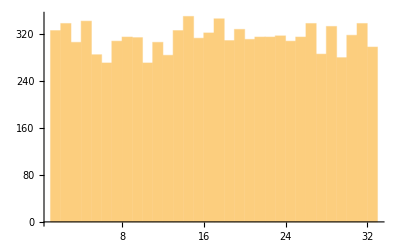

```mathematica
Histogram[Flatten[Import["Program Files/test.txt","Data"]]]
```

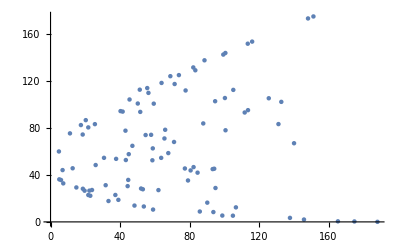

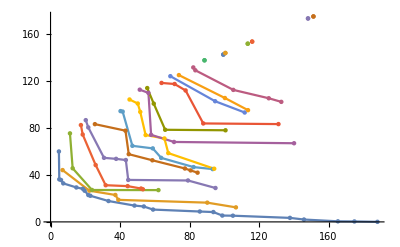

```mathematica
data=Import["Program Files/test2.txt","Data"];
ListPlot[data[[All,;;2]],PlotStyle->PointSize[0.008]]
sorteddata=Table[Select[data,#[[3]]==i&][[All,;;2]],{i,Max[data[[All,3]]]}];
Show[ListLinePlot[sorteddata],ListPlot[sorteddata,PlotStyle->PointSize[0.008]]]
```

```mathematica
ngen=10;
data=Import["Program Files/test3.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,{3,4}]],{i,1,ngen}];
Manipulate[Show[ParametricPlot[{4 x^2+4 y^2,(x-5)^2+(y-5)^2},{x,-10,10},{y,-10,10},Mesh->None,BoundaryStyle->None],ListPlot[gendata[[i]],PlotStyle->{PointSize[0.01],Red}],PlotRange->{{Min[gendata[[-1,All,1]]],Max[gendata[[-1,All,1]]]},{Min[gendata[[-1,All,2]]],Max[gendata[[-1,All,2]]]}},AspectRatio->1/GoldenRatio],{i,1,ngen,1}]
```

```mathematica
Manipulate[Show[ParametricPlot[{4 x^2+4 y^2,(x-5)^2+(y-5)^2},{x,-10,10},{y,-10,10},Mesh->None,BoundaryStyle->None],ListPlot[gendata[[i]],PlotStyle->{PointSize[0.008],Red}],PlotRange->{{Min[data[[All,3]]],Max[data[[All,3]]]},{Min[data[[All,4]]],Max[data[[All,4]]]}}],{i,1,ngen,1}]
```

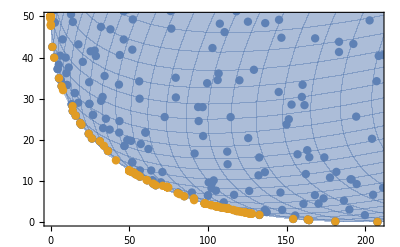

```mathematica
Show[ParametricPlot[{4 x^2+4 y^2,(x-5)^2+(y-5)^2},{x,-10,10},{y,-10,10},Mesh->None,BoundaryStyle->None],ListPlot[{gendata[[1]],gendata[[-1]]},PlotStyle->PointSize[0.015]],PlotRange->{{Min[gendata[[-1,All,1]]],Max[gendata[[-1,All,1]]]},{Min[gendata[[-1,All,2]]],Max[gendata[[-1,All,2]]]}},AspectRatio->1/GoldenRatio]
```

```mathematica
ngen=11;
data=Import["Program Files/test4.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,{4,5}]],{i,1,ngen}];
Manipulate[ListPlot[gendata[[i]],PlotStyle->{PointSize[0.01],Red},PlotRange->{{Min[gendata[[-1,All,1]]],Max[gendata[[-1,All,1]]]},{Min[gendata[[-1,All,2]]],Max[gendata[[-1,All,2]]]}},AspectRatio->1/GoldenRatio],{i,1,ngen,1}]
```

```mathematica
Manipulate[ListPlot[gendata[[i]],PlotStyle->{PointSize[0.01],Red},PlotRange->{{Min[gendata[[1,All,1]]],Max[gendata[[1,All,1]]]},{Min[gendata[[1,All,2]]],Max[gendata[[1,All,2]]]}},AspectRatio->1/GoldenRatio],{i,1,ngen,1}]
```

# Data

```mathematica
duration=0.25;imagedpi=150;
```

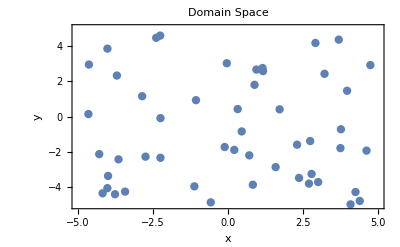

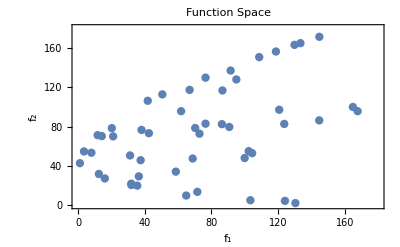

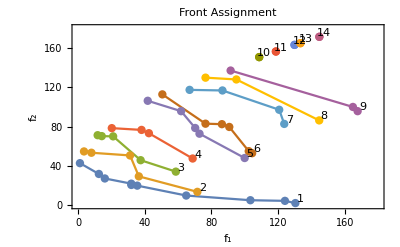

```mathematica
ngen=1+1;
data=Import["Program Files/ranking.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,All]],{i,1,ngen}];
range=180;
sorteddata=Table[Select[gendata[[1]],#[[6]]==i&],{i,Max[gendata[[1,All,6]]]}];
ListPlot[gendata[[1,All,1;;2]],PlotStyle->PointSize[0.015],PlotRange->{{-5,5},{-5,5}},BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Domain Space",FrameLabel->{x,y}]
Export["Plots/domainspace.png",%,ImageResolution->imagedpi];
ListPlot[gendata[[1,All,3;;4]],PlotStyle->PointSize[0.015],PlotRange->{{0,range},{0,range}},BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Function Space",FrameLabel->{Subscript[f, 1],Subscript[f, 2]}]
Export["Plots/functionspace.png",%,ImageResolution->imagedpi];
offx=3;offy=4;
Show[ListLinePlot[sorteddata[[All,All,3;;4]],PlotRange->{{0,range},{0,range}}],ListPlot[sorteddata[[All,All,3;;4]],PlotStyle->PointSize[0.015],PlotRange->{{0,170},{0,170}}],Graphics[Table[Text[i,{sorteddata[[i,1,3]]+offx,sorteddata[[i,1,4]]+offy}],{i,Max[gendata[[1,All,6]]]}]],BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Front Assignment",FrameLabel->{Subscript[f, 1],Subscript[f, 2]}]
Export["Plots/fronts.png",%,ImageResolution->imagedpi];
```

```mathematica
ngen=10+1;
f[{x_,y_}]:=-20*Exp[-0.2*Sqrt[0.5*(x^2+y^2)]]-Exp[0.5*(Cos[2*π*x]+Cos[2*π*y])]+Exp[1]+20;
data=Import["Program Files/ackley.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,All]],{i,1,ngen}];
(*Manipulate[Show[Plot3D[f[{x,y}],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",PlotStyle->Opacity[0.6],MeshStyle->Opacity[0.4],BoundaryStyle->Opacity[0.4],PlotTheme->"Default"],ListPointPlot3D[gendata[[i,All,1;;3]],PlotStyle->{PointSize[0.03],Blue}],PlotLabel->"Ackley's Function\nGeneration "<>IntegerString[i-1,10],BaseStyle->{FontFamily->Times},BoxRatios->{1,1,0.8},ViewPoint->{1,-2,1}],{i,1,11,1}]*)
plots=Table[Show[Plot3D[f[{x,y}],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",PlotStyle->Opacity[0.6],MeshStyle->Opacity[0.4],BoundaryStyle->Opacity[0.4],PlotTheme->"Default"],ListPointPlot3D[gendata[[i,All,1;;3]],PlotStyle->{PointSize[0.03],Blue}],PlotLabel->"Ackley's Function\nGeneration "<>IntegerString[i-1,10],BaseStyle->{FontFamily->Times},BoxRatios->{1,1,0.8},ViewPoint->{1,-2,1}],{i,1,11,1}];
Export["Plots/ackley.gif",plots,"DisplayDurations"->duration,ImageResize->imagedpi];
Export["Plots/ackley0.png",plots[[1]],"DisplayDurations"->duration,ImageResize->imagedpi];
Export["Plots/ackley10.png",plots[[-1]],"DisplayDurations"->duration,ImageResize->imagedpi];
```

```mathematica
ngen=20+1;
data=Import["Program Files/kursawe.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,{4,5}]],{i,1,ngen}];
(*Manipulate[ListPlot[gendata[[i]],PlotTheme->"Classic",PlotRange->{{Min[gendata[[j,All,1]]],Max[gendata[[j,All,1]]]},{Min[gendata[[j,All,2]]],Max[gendata[[j,All,2]]]}},AspectRatio->1/GoldenRatio,Frame->True,Axes->False,FrameLabel->{Subscript[f, 1],Subscript[f, 2]},GridLines->Automatic,GridLinesStyle->Opacity[0.2],PlotLabel->"Kursawe Function\nGeneration "<>IntegerString[i,10]
],{{i,1,"Generation"},1,ngen,1},{{j,1,"Zoom"},{1,-1}}]*)
plots=Table[ListPlot[gendata[[i]],PlotTheme->"Classic",PlotRange->{{Min[gendata[[j,All,1]]],Max[gendata[[j,All,1]]]},{Min[gendata[[j,All,2]]],Max[gendata[[j,All,2]]]}},AspectRatio->1/GoldenRatio,Frame->True,Axes->False,FrameLabel->{Subscript[f, 1],Subscript[f, 2]},GridLines->Automatic,GridLinesStyle->Opacity[0.2],PlotLabel->"Kursawe Function\nGeneration "<>IntegerString[i-1,10]
],{i,1,ngen,1},{j,{1,-1}}];
Export["kursaweout.gif",plots[[All,1]],"DisplayDurations"->duration,ImageResolution->imagedpi];
Export["Plots/kursaweout0.png",plots[[1,1]],ImageResolution->imagedpi];
Export["Plots/kursaweout20.png",plots[[-1,1]],ImageResolution->imagedpi];
Export["Plots/kursawein.gif",plots[[All,2]],"DisplayDurations"->duration,ImageResolution->imagedpi];
Export["Plots/kursawein0.png",plots[[1,2]],ImageResolution->imagedpi];
Export["Plots/kursawein20.png",plots[[-1,2]],ImageResolution->imagedpi];
```

```mathematica
ngen=20+1;
data=Import["Program Files/binhkorn.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,{3,4}]],{i,1,ngen}];
(*Manipulate[ListPlot[gendata[[i]],PlotTheme->"Classic",PlotRange->{{Min[gendata[[j,All,1]]],Max[gendata[[j,All,1]]]},{Min[gendata[[j,All,2]]],Max[gendata[[j,All,2]]]}},AspectRatio->1/GoldenRatio,Frame->True,Axes->False,FrameLabel->{Subscript[f, 1],Subscript[f, 2]},GridLines->Automatic,GridLinesStyle->Opacity[0.2],PlotLabel->"Kursawe Function\nGeneration "<>IntegerString[i,10]
],{{i,1,"Generation"},1,ngen,1},{{j,1,"Zoom"},{1,-1}}]*)
plots=Table[ListPlot[gendata[[i]],PlotTheme->"Classic",PlotRange->{{Min[gendata[[j,All,1]]],Max[gendata[[j,All,1]]]},{Min[gendata[[j,All,2]]],Max[gendata[[j,All,2]]]}},AspectRatio->1/GoldenRatio,Frame->True,Axes->False,FrameLabel->{Subscript[f, 1],Subscript[f, 2]},GridLines->Automatic,GridLinesStyle->Opacity[0.2],PlotLabel->"Binh and Korn Function\nGeneration "<>IntegerString[i-1,10]
],{i,1,ngen/2+1,1},{j,{1,-1}}];
Export["Plots/binhkornout.gif",plots[[All,1]],"DisplayDurations"->2*duration,ImageResolution->imagedpi];
Export["Plots/binhkornout0.png",plots[[1,1]],ImageResolution->imagedpi];
Export["Plots/binhkornout10.png",plots[[-1,1]],ImageResolution->imagedpi];
Export["Plots/binhkornin.gif",plots[[All,2]],"DisplayDurations"->2*duration,ImageResolution->imagedpi];
Export["Plots/binhkornin0.png",plots[[1,2]],ImageResolution->imagedpi];
Export["Plots/binhkornin10.png",plots[[-1,2]],ImageResolution->imagedpi];
```

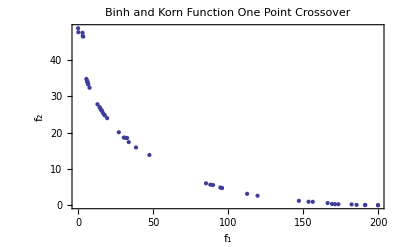

Plots/oneptcross.png

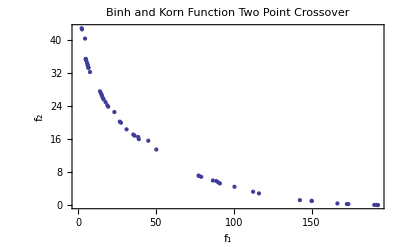

Plots/twoptcross.png

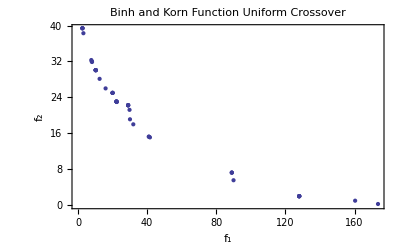

Plots/unifcross.png

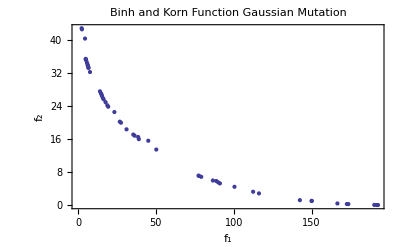

Plots/mutgauss.png

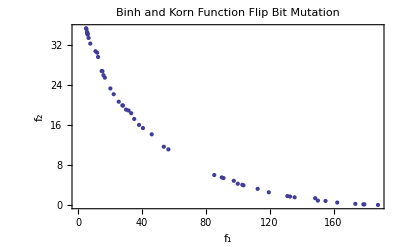

Plots/mutflipbit.png

```mathematica
ngen=5+1;
data=Import["Results/Operator Comparisons/oneptcross.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,All]],{i,1,ngen}];
ListPlot[gendata[[-1,All,3;;4]],PlotTheme->"Classic",BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Binh and Korn Function\nOne Point Crossover",FrameLabel->{Subscript[f, 1],Subscript[f, 2]}]
Export["Plots/oneptcross.png",%,ImageResolution->imagedpi]
data=Import["Results/Operator Comparisons/twoptcross.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,All]],{i,1,ngen}];
ListPlot[gendata[[-1,All,3;;4]],PlotTheme->"Classic",BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Binh and Korn Function\nTwo Point Crossover",FrameLabel->{Subscript[f, 1],Subscript[f, 2]}]
Export["Plots/twoptcross.png",%,ImageResolution->imagedpi]
data=Import["Results/Operator Comparisons/unifcross.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,All]],{i,1,ngen}];
ListPlot[gendata[[-1,All,3;;4]],PlotTheme->"Classic",BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Binh and Korn Function\nUniform Crossover",FrameLabel->{Subscript[f, 1],Subscript[f, 2]}]
Export["Plots/unifcross.png",%,ImageResolution->imagedpi]
data=Import["Results/Operator Comparisons/mutgauss.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,All]],{i,1,ngen}];
ListPlot[gendata[[-1,All,3;;4]],PlotTheme->"Classic",BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Binh and Korn Function\nGaussian Mutation",FrameLabel->{Subscript[f, 1],Subscript[f, 2]}]
Export["Plots/mutgauss.png",%,ImageResolution->imagedpi]
data=Import["Results/Operator Comparisons/mutflipbit.txt","Data"];
gendata=Table[data[[(i-1)*Length[data]/ngen+1;;i*Length[data]/ngen,All]],{i,1,ngen}];
ListPlot[gendata[[-1,All,3;;4]],PlotTheme->"Classic",BaseStyle->{FontFamily->Times},Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Binh and Korn Function\nFlip Bit Mutation",FrameLabel->{Subscript[f, 1],Subscript[f, 2]}]
Export["Plots/mutflipbit.png",%,ImageResolution->imagedpi]
```